```mathematica
qubit0:={{1},{0}}
qubit1:={{0},{1}}
```

```mathematica
k0000:=KroneckerProduct[KroneckerProduct[KroneckerProduct[qubit0,qubit0],qubit0],qubit0]
k0111:=KroneckerProduct[KroneckerProduct[KroneckerProduct[qubit0,qubit1],qubit1],qubit1]
k1010:=KroneckerProduct[KroneckerProduct[KroneckerProduct[qubit1,qubit0],qubit1],qubit0]
k1101:=KroneckerProduct[KroneckerProduct[KroneckerProduct[qubit1,qubit1],qubit0],qubit1]
b0000:=Transpose[k0000]
b0111:=Transpose[k0111]
b1010:=Transpose[k1010]
b1101:=Transpose[k1101]
k000:=KroneckerProduct[KroneckerProduct[qubit0,qubit0],qubit0]
k111:=KroneckerProduct[KroneckerProduct[qubit1,qubit1],qubit1]
k010:=KroneckerProduct[KroneckerProduct[qubit0,qubit1],qubit0]
k101:=KroneckerProduct[KroneckerProduct[qubit1,qubit0],qubit1]
b000:=Transpose[k000]
b111:=Transpose[k111]
b010:=Transpose[k010]
b101:=Transpose[k101]
k011:=KroneckerProduct[KroneckerProduct[qubit0,qubit1],qubit1]
k100:=KroneckerProduct[KroneckerProduct[qubit1,qubit0],qubit0]
b011:=Transpose[k011]
b100:=Transpose[k100]
```

```mathematica
H[g_]:=1/(2g^2){{0,0,0,0,0,0,0,-2,0,0,0,0,0,-2,0,0},{0,3g^4/4,0,0,0,0,-2,0,0,0,0,0,-2,0,0,0},{0,0,3g^4/2,0,0,-2,0,0,0,0,0,0,0,0,0,-1/2},{0,0,0,9g^4/4,-2,0,0,0,0,0,0,0,0,0,-1/2,0},{0,0,0,-2,3g^4/4,0,0,0,0,-2,0,0,0,0,0,0},{0,0,-2,0,0,3g^4/2,0,0,-2,0,0,0,0,0,0,0},{0,-2,0,0,0,0,9g^4/4,0,0,0,0,-1/2,0,0,0,0},{-2,0,0,0,0,0,0,3g^4,0,0,-1/2,0,0,0,0,0},{0,0,0,0,0,-2,0,0,3g^4/2,0,0,0,0,0,0,-1/2},{0,0,0,0,-2,0,0,0,0,9g^4/4,0,0,0,0,-1/2,0},{0,0,0,0,0,0,0,-1/2,0,0,3g^4,0,0,-1/2,0,0},{0,0,0,0,0,0,-1/2,0,0,0,0,15g^4/4,-1/2,0,0,0},{0,-2,0,0,0,0,0,0,0,0,0,-1/2,9g^4/4,0,0,0},{-2,0,0,0,0,0,0,0,0,0,-1/2,0,0,3g^4,0,0},{0,0,0,-1/2,0,0,0,0,0,-1/2,0,0,0,0,15g^4/4,0},{0,0,-1/2,0,0,0,0,0,-1/2,0,0,0,0,0,0,9g^4/2}}+500IdentityMatrix[16]
```

```mathematica
GS[g_]:=Part[Eigenvectors[H[g]],16]
```

```mathematica
ρ[g_]:=KroneckerProduct[GS[g],Transpose[GS[g]]]
```

```mathematica
RDM[g_]:=Part[GS[g],1]^2k000.b000+Part[GS[g],1]Part[GS[g],8]k000.b111+Part[GS[g],1]Part[GS[g],8]k111.b000+Part[GS[g],8]^2k111.b111+Part[GS[g],11]^2k010.b010+Part[GS[g],11]Part[GS[g],14]k010.b101+Part[GS[g],14]Part[GS[g],11]k101.b010+Part[GS[g],14]^2k101.b101
```

```mathematica
S[g_]:=-Part[Eigenvalues[RDM[g]],1]Log[2,Part[Eigenvalues[RDM[g]],1]]-Part[Eigenvalues[RDM[g]],2]Log[2,Part[Eigenvalues[RDM[g]],2]]-Part[Eigenvalues[RDM[g]],3]Log[2,Part[Eigenvalues[RDM[g]],3]]
```

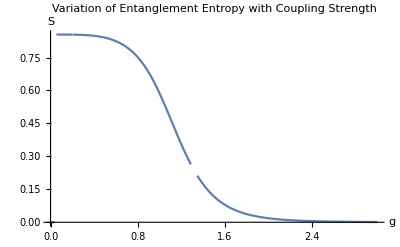

```mathematica
Plot[S[g],{g,0,3},AxesLabel->{"g","S"},PlotLabel->"Variation of Entanglement Entropy with Coupling Strength"]
```

```mathematica
Manipulate[S[g],{g,0.053995022434,3, Appearance->"Labeled"}]
```

Need to set up system to get Hamiltonian and ground state for n plaquettes in 1-d chain. Do this first by converting to a 1-d chain of 2-index tensors containing three links from the plaquette, then determine the ground state using gates + SVD? Check with Anthony to see how they did this even if the code doesn’t have any comments. Learn tensor networks! How does ‘blocking’ work? Looks from the paper like three links get combined and electric field operator goes to the fourth link?
Paper describes setting up witness operators for NALG theories. Works same as most witness operators -- not calculation of specific entanglement, but just determines how entangled they are via expectation value. 
Then need to use the ground state to calculate the entanglement entropy for m<n plaquettes.
Needs to convert to tensor network, extract the ground state wavefunction, convert back to plaquettes, and then do the actual calculation.
Do by switching to two-index tensors; one counts possible states, other just lists all the states in vector form rather than as a matrix.

```mathematica
reducedH[g_]:=1/(2g^2){{0,-2,0,-2},{-2,3g^4,-1/2,0},{0,-1/2,3g^4,-1/2},{-2,0,-1/2,3g^4}}+500IdentityMatrix[4]
nthstate[g_,n_]:=Part[Eigenvectors[reducedH[g]],4-n]
```

```mathematica
rRDM[g_]:=Part[rGS[g],1]^2k000.b000+Part[rGS[g],1]Part[rGS[g],2]k000.b111+Part[rGS[g],1]Part[rGS[g],2]k111.b000+Part[rGS[g],2]^2k111.b111+Part[rGS[g],3]^2k010.b010+Part[rGS[g],3]Part[rGS[g],4]k010.b101+Part[rGS[g],3]Part[rGS[g],4]k101.b010+Part[rGS[g],4]^2k101.b101
```

```mathematica
ψ[g_,p_]:=p nthstate[g,0]+(1-p)nthstate[g,1]
```

```mathematica
ρ[g_,p_]:=KroneckerProduct[ψ[g,p],Transpose[ψ[g,p]]]
```

```mathematica
twoStateRDM[g_,p_]:=Part[ψ[g,p],1]^2k000.b000+Part[ψ[g,p],1]Part[ψ[g,p],2]k000.b111+Part[ψ[g,p],1]Part[ψ[g,p],2]k111.b000+Part[ψ[g,p],2]^2k111.b111+Part[ψ[g,p],3]^2k010.b010+Part[ψ[g,p],3]Part[ψ[g,p],4]k010.b101+Part[ψ[g,p],3]Part[ψ[g,p],4]k101.b010+Part[ψ[g,p],4]^2k101.b101
twoStateRDM2[g_,p_]:=Part[ψ[g,p],1]^2k000.b000+Part[ψ[g,p],1]Part[ψ[g,p],4]k000.b111+Part[ψ[g,p],1]Part[ψ[g,p],4]k111.b000+Part[ψ[g,p],4]^2k111.b111+Part[ψ[g,p],2]^2k011.b011+Part[ψ[g,p],2]Part[ψ[g,p],3]k011.b100+Part[ψ[g,p],2]Part[ψ[g,p],3]k011.b100+Part[ψ[g,p],3]^2k100.b100
```

```mathematica
rSee[g_,p_]:=-Sum[Part[Eigenvalues[twoStateRDM[g,p]],i]Log[2,Part[Eigenvalues[twoStateRDM[g,p]],i]],{i,1,2}]
rSee2[g_,p_]:=-Sum[Part[Eigenvalues[twoStateRDM2[g,p]],i]Log[2,Part[Eigenvalues[twoStateRDM2[g,p]],i]],{i,1,2}]
```

```mathematica
rS[g_,p_]:=-Sum[Part[Eigenvalues[ρ[g,p]],i]Log[2,Part[Eigenvalues[ρ[g,p]],i]],{i,1,2}]
```

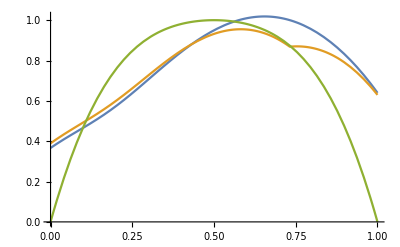

```mathematica
Plot[{Re[rSee[Sqrt[0.9],p]],Re[rSee2[Sqrt[0.9],p]],2rS[Sqrt[0.9],p]},{p,0,1}]
```

```mathematica
rS[Sqrt[0.9],0.5]
```

0.5